```mathematica
ClearAll["Global`*"];
Off[General::spell, General::spell1]
```

```mathematica
Clear[x,a,b,c];
f=a x^2+b x + c;
```

```mathematica
f
```

c+b x+a x^2

```mathematica
f/.{a->1,b->2,c->4,x->4}
```

28

```mathematica
a=1;b=2;c=3;
f
```

3+2 x+x^2

```mathematica
x=4;
f
```

16 a+4 b+c

```mathematica
D[f,x]
```

General::ivar: 4 is not a valid variable.

∂_4 (16 a+4 b+c)

```mathematica
?x
```

```mathematica
Clear[x];
D[f,x]
```

b+2 a x

```mathematica
Clear[a,b,c,x]
```

```mathematica
parameters["f"]={a->1,b->2,c->3};
```

```mathematica
f/.parameters["f"]
```

3+2 x+x^2

```mathematica
f/.x->2/.parameters["f"]
```

11

```mathematica
f=1/(1+1/(1+z^2))
```

1/(1+1/(1+z^2))

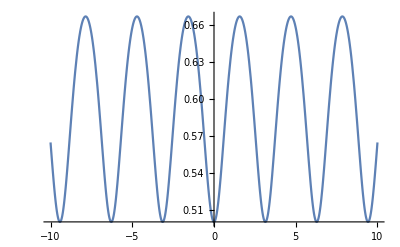

```mathematica
Plot[f/.z->Sin[x],{x,-10,10}]
```

```mathematica
Clear[g];
g[x_]=x^2 Exp[-x^2]
```

ⅇ^(-x^2) x^2

```mathematica
g[x]
```

ⅇ^(-x^2) x^2

```mathematica
g[y]
```

ⅇ^(-y^2) y^2

```mathematica
g[2]
```

4/ⅇ^4

```mathematica
g[2.]
```

0.0732626

```mathematica
g["stuff"]
```

stuff^2 ⅇ^(-stuff^2)

```mathematica
g["stuff"]//FullForm
```

Times[Power["stuff",2],Power[E,Times[-1,Power["stuff",2]]]]

```mathematica
g[g[z]]
```

ⅇ^(-2 z^2-ⅇ^(-2 z^2) z^4) z^4

```mathematica
g[x_,y_]=x^(2+y)Exp[-x^2]
```

ⅇ^(-x^2) x^(2+y)

```mathematica
{g[x,y],g[x,0],g[x,2],g[x,-4],g[2,2],g[x,"stuff"]}
```

{ⅇ^(-x^2) x^(2+y),ⅇ^(-x^2) x^2,ⅇ^(-x^2) x^4,(ⅇ^(-x^2))/x^2,16/ⅇ^4,ⅇ^(-x^2) x^(2+stuff)}

```mathematica
g[x]
```

ⅇ^(-x^2) x^2

```mathematica
?g
```

```mathematica
g[x,y,z]
```

g[x,y,z]

```mathematica
g[x_]=π
```

π

```mathematica
g["stuff"]
```

π

```mathematica
h[_]=π
```

π

```mathematica
h["stuff"]
```

π

```mathematica
area["rectange",b_,h_]=b h
```

b h

```mathematica
area["rectange",2,3]
```

6

```mathematica
area["r",2,3]
```

area[r,2,3]

```mathematica
PlotDerivative[f_,{x_,xmin_,xmax_}]:=Plot[Evaluate[D[f[x],x]],{x,xmin,xmax}]
```

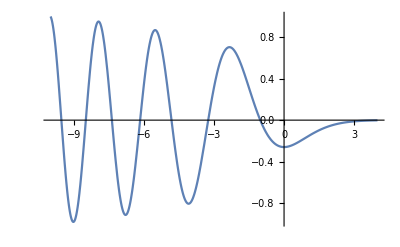

```mathematica
PlotDerivative[AiryAi,{x,-10,4}]
```

```mathematica
sbessj[n_,z_]:=√(π/2)z^(-1/2)BesselJ[n+1/2,z];
sbessy[n_,z_]:=√(π/2)z^(-1/2)BesselY[n+1/2,z];
```

```mathematica
plotsbess[n_,xmin_,xmax_]:=Plot[{sbessj[n,x],sbessy[n,x]},{x,xmin,xmax}]
```

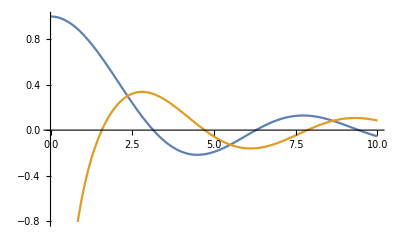

```mathematica
plotsbess[0,0.001,10]
```

```mathematica
logStirling1[n_]:=n Log[n] - n;
logStirling2[n_]:=logStirling1[n]+1/2 Log[2 π n];
logStirling3[n_]:=logStirling2[n]+1/(12 n);
```

```mathematica
logStirling1[2]
```

-2+2 Log[2]

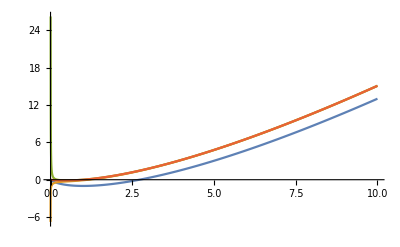

```mathematica
Plot[{logStirling1[n],logStirling2[n],logStirling3[n],Log[Factorial[n]]},{n,0,10}]
```

```mathematica
Clear[f,a,b,c,d];
f[a_,b_,c_,d_]:=d a^(b^c)
```

```mathematica
f[a,b,c,d]
```

a^(b^c) d

```mathematica
argumentList={a,b,c}
```

{a,b,c}

```mathematica
f[argumentList,d]
```

f[{a,b,c},d]

```mathematica
argumentSequence=Sequence@@argumentList
```

Sequence[a,b,c]

```mathematica
f[argumentSequence,d]
```

a^(b^c) d

```mathematica
Clear[g];
g[stuff,argumentSequence,moreStuff]
```

g[stuff,a,b,c,moreStuff]

```mathematica
Clear[f,n,m];
f[n_,m_]:=(temp=Expand[(a+b x)^m];Coefficient[temp,x,n])
```

```mathematica
f[3,10]
```

120 a^7 b^3

```mathematica
temp
```

a^10+10 a^9 b x+45 a^8 b^2 x^2+120 a^7 b^3 x^3+210 a^6 b^4 x^4+252 a^5 b^5 x^5+210 a^4 b^6 x^6+120 a^3 b^7 x^7+45 a^2 b^8 x^8+10 a b^9 x^9+b^10 x^10

```mathematica
h=Function[x,a x^2+b x + c]
h[Sin[ϕ]^2]
h[h[y]]
```

Function[x,a x^2+b x+c]

c+b Sin[ϕ]^2+a Sin[ϕ]^4

c+b (c+b y+a y^2)+a (c+b y+a y^2)^2

```mathematica
?h
```

```mathematica
h[2]
```

4 a+2 b+c

```mathematica
x="something";
g=Function[x,x^2]
```

Function[x,x^2]

```mathematica
g[2]
```

4

```mathematica
Clear[g];
g[x_]:=x^2
```

```mathematica
x
```

something

```mathematica
g[2]
```

4

```mathematica
g[y]
```

y^2

```mathematica
h[a]
```

a^3+a b+c

```mathematica
a=2
```

2

```mathematica
h[z]
```

c+b z+2 z^2

```mathematica
Clear[a];
h[z]
```

c+b z+a z^2

```mathematica
Clear[f1,f2,g,y,z];
f1[x_]=Expand[x];
f2[y_]=Expand[y];
g=Function[x,Expand[x]];
```

```mathematica
f1[(y+z)^2]
```

something

```mathematica
f2[(y+z)^2]
```

(y+z)^2

```mathematica
g[(y+z)^2]
```

y^2+2 y z+z^2

```mathematica
D[h[y],y]
```

b+2 a y

```mathematica
h'
```

Function[x,b+2 a x]

```mathematica
{h'[stuff],h'[2/3]}
```

{b+2 a stuff,(4 a)/3+b}

```mathematica
Clear[g];
g=Function[x,μ x (1-x)]
```

Function[x,μ x (1-x)]

```mathematica
Clear[x]
```

```mathematica
NestList[g,x,4]
```

{x,(1-x) x μ,(1-x) x μ^2 (1-(1-x) x μ),(1-x) x μ^3 (1-(1-x) x μ) (1-(1-x) x μ^2 (1-(1-x) x μ)),(1-x) x μ^4 (1-(1-x) x μ) (1-(1-x) x μ^2 (1-(1-x) x μ)) (1-(1-x) x μ^3 (1-(1-x) x μ) (1-(1-x) x μ^2 (1-(1-x) x μ)))}

```mathematica
s=Function[{x,y,z},x y^-3 Erf[z]]
```

Function[{x,y,z},(x Erf[z])/y^3]

```mathematica
Clear[x];
s[x,1/y,4]
```

x y^3 Erf[4]

```mathematica
s[x,x,x]
```

Erf[x]/x^2

```mathematica
s[1]
```

Function::fpct: Too many parameters in {x,y,z} to be filled from Function[{x,y,z},(x Erf[z])/y^3][1].

Function[{x,y,z},(x Erf[z])/y^3][1]

```mathematica
x="stuff";y="more stuff";
h=Function[{x,y},x+y]
```

Function[{x,y},x+y]

```mathematica
h[x,y]
```

more stuff+stuff

```mathematica
Clear[a,b];
h[a,b]
```

a+b

```mathematica
Clear[x,y,z];
Function[{x,y,z},x y^2 z^3][z,x,y]
```

x^2 y^3 z

```mathematica
Clear[a,b,c]
```

```mathematica
Function[x,a x^2+b x + c]
```

Function[x,a x^2+b x+c]

```mathematica
Function[x,a x^2+b x + c][q]
```

c+b q+a q^2

```mathematica
Function[x,a x^2+b x + c][Tanh[y]]
```

c+b Tanh[y]+a Tanh[y]^2

```mathematica
Function[x,a x^2+b x + c]@Tanh[y]
```

c+b Tanh[y]+a Tanh[y]^2

```mathematica
Clear[a,b,c,x];
a #^2+b # + c & [x]
```

c+b x+a x^2

```mathematica
h=a #^2+b #+c &
```

a #1^2+b #1+c&

```mathematica
h[stuff]
```

c+b stuff+a stuff^2

```mathematica
g = (#1 + 2#2) Exp[-#3^2]&;
```

```mathematica
g[x,y,z]
```

ⅇ^(-z^2) (x+2 y)

```mathematica
Clear[f1,f2];
f1=Tan;
f2=f1'
```

Sec[#1]^2&

```mathematica
{f1[30 Degree],f2[30 Degree]}
```

{1/(√3),4/3}

```mathematica
Clear[x];
DerivF=Function[f,D[f[x],x]]
```

Function[f,∂_x f[x]]

```mathematica
DerivF[2 x^2]
```

4 x

```mathematica
args={x,y,z};
```

```mathematica
g@@args
```

ⅇ^(-z^2) (x+2 y)

```mathematica
g@@{x,y,z,"more stuff"}
```

ⅇ^(-z^2) (x+2 y)

```mathematica
g@@{x,y}
```

Function::slotn: Slot number 3 in (#1+2 #2) Exp[-#3^2]& cannot be filled from ((#1+2 #2) Exp[-#3^2]&)[x,y].

ⅇ^(-#3^2) (x+2 y)

```mathematica
f=#^2 Cos[#]&
```

#1^2 Cos[#1]&

```mathematica
f[2]
```

4 Cos[2]

```mathematica
Expand[(a+b x)^13]//Coefficient[#,x,3]&
```

286 a^10 b^3

```mathematica
Clear[f];
f[n_,m_]:=Expand[(a+b x)^m]//Coefficient[#,x,n]&
```

```mathematica
f[3,13]
```

286 a^10 b^3

```mathematica
?f
```

```mathematica
swing[θ0_,ω0_,tmin_,tmax_]:=NDSolve[
{θ''[t]==-Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ,{t,tmin,tmax}]
```

```mathematica
swing[(3π)/4,0,0,10]
```

{{θ→InterpolatingFunction[…]}}

```mathematica
swing1[t]=θ[t]/.swing[(3π)/4,0,0,10][[1]]
```

InterpolatingFunction[…][t]

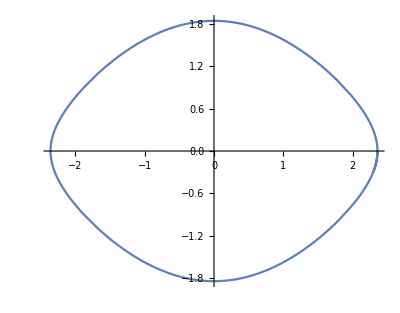

```mathematica
ParametricPlot[Evaluate[{swing1[t],D[swing1[t],t]}],
{t,0,10},AspectRatio->Automatic]
```

```mathematica
factorial[0]=1;
factorial[n_]:=n factorial[n-1]
```

```mathematica
Table[factorial[n],{n,0,10}]
```

{1,1,2,6,24,120,720,5040,40320,362880,3628800}

```mathematica
Trace[factorial[10]]
```

{factorial[10],10 factorial[10-1],{{10-1,9},factorial[9],9 factorial[9-1],{{9-1,8},factorial[8],8 factorial[8-1],{{8-1,7},factorial[7],7 factorial[7-1],{{7-1,6},factorial[6],6 factorial[6-1],{{6-1,5},factorial[5],5 factorial[5-1],{{5-1,4},factorial[4],4 factorial[4-1],{{4-1,3},factorial[3],3 factorial[3-1],{{3-1,2},factorial[2],2 factorial[2-1],{{2-1,1},factorial[1],1 factorial[1-1],{{1-1,0},factorial[0],1},1 1,1},2 1,2},3 2,6},4 6,24},5 24,120},6 120,720},7 720,5040},8 5040,40320},9 40320,362880},10 362880,3628800}

```mathematica
factorial2[0]=1;
factorial2[n_]:=factorial[n]=n factorial2[n-1]
```

```mathematica
factorial[100]//Timing
```

{0.000182,93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000}

```mathematica
factorial2[100]//Timing
```

{0.000259,93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000}

```mathematica
factorial2[100]//Timing
```

{0.000417,93326215443944152681699238856266700490715968264381621468592963895217599993229915608941463976156518286253697920827223758251185210916864000000000000000000000000}

```mathematica
Trace[factorial2[10]]
```

{factorial2[10],factorial[10]=10 factorial2[10-1],{{{10-1,9},factorial2[9],factorial[9]=9 factorial2[9-1],{{{9-1,8},factorial2[8],factorial[8]=8 factorial2[8-1],{{{8-1,7},factorial2[7],factorial[7]=7 factorial2[7-1],{{{7-1,6},factorial2[6],factorial[6]=6 factorial2[6-1],{{{6-1,5},factorial2[5],factorial[5]=5 factorial2[5-1],{{{5-1,4},factorial2[4],factorial[4]=4 factorial2[4-1],{{{4-1,3},factorial2[3],factorial[3]=3 factorial2[3-1],{{{3-1,2},factorial2[2],factorial[2]=2 factorial2[2-1],{{{2-1,1},factorial2[1],factorial[1]=1 factorial2[1-1],{{{1-1,0},factorial2[0],1},1 1,1},factorial[1]=1,1},2 1,2},factorial[2]=2,2},3 2,6},factorial[3]=6,6},4 6,24},factorial[4]=24,24},5 24,120},factorial[5]=120,120},6 120,720},factorial[6]=720,720},7 720,5040},factorial[7]=5040,5040},8 5040,40320},factorial[8]=40320,40320},9 40320,362880},factorial[9]=362880,362880},10 362880,3628800},factorial[10]=3628800,3628800}

```mathematica
?factorial
```

```mathematica
?factorial2
```

```mathematica
factorial[1000]//Timing
```

{0.000913,402387260077093773543702433923003985719374864210714632543799910429938512398629020592044208486969404800479988610197196058631666872994808558901323829669944590997424504087073759918823627727188732519779505950995276120874975462497043601418278094646496291056393887437886487337119181045825783647849977012476632889835955735432513185323958463075557409114262417474349347553428646576611667797396668820291207379143853719588249808126867838374559731746136085379534524221586593201928090878297308431392844403281231558611036976801357304216168747609675871348312025478589320767169132448426236131412508780208000261683151027341827977704784635868170164365024153691398281264810213092761244896359928705114964975419909342221566832572080821333186116811553615836546984046708975602900950537616475847728421889679646244945160765353408198901385442487984959953319101723355556602139450399736280750137837615307127761926849034352625200015888535147331611702103968175921510907788019393178114194545257223865541461062892187960223838971476088506276862967146674697562911234082439208160153780889893964518263243671616762179168909779911903754031274622289988005195444414282012187361745992642956581746628302955570299024324153181617210465832036786906117260158783520751516284225540265170483304226143974286933061690897968482590125458327168226458066526769958652682272807075781391858178889652208164348344825993266043367660176999612831860788386150279465955131156552036093988180612138558600301435694527224206344631797460594682573103790084024432438465657245014402821885252470935190620929023136493273497565513958720559654228749774011413346962715422845862377387538230483865688976461927383814900140767310446640259899490222221765904339901886018566526485061799702356193897017860040811889729918311021171229845901641921068884387121855646124960798722908519296819372388642614839657382291123125024186649353143970137428531926649875337218940694281434118520158014123344828015051399694290153483077644569099073152433278288269864602789864321139083506217095002597389863554277196742822248757586765752344220207573630569498825087968928162753848863396909959826280956121450994871701244516461260379029309120889086942028510640182154399457156805941872748998094254742173582401063677404595741785160829230135358081840096996372524230560855903700624271243416909004153690105933983835777939410970027753472000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000}

```mathematica
ClearAll[factorial2]
```

```mathematica
?factorial2
```

```mathematica
Clear[f];
f[x_Integer]:=x^2;
f[x_Real]:=x^3;
f[x_Complex]:=Abs[x]^2;
f[x_List]:=(Plus@@x)^2
```

```mathematica
{f[2],f[2.]}
```

{4,8.}

```mathematica
f[1+3I]
```

10

```mathematica
f[{2,3}]
```

25

```mathematica
f[a]
```

f[a]

```mathematica
f[x_Symbol]:="whatever you want"
```

```mathematica
f[{2,3}]
```

25

```mathematica
f[a]
```

whatever you want

```mathematica
f[a^2]
```

f[a^2]

```mathematica
{MatchQ[a,_Symbol],MatchQ[a^2,_Symbol]}
```

{True,False}

```mathematica
?f
```

```mathematica
Clear[f];
```

```mathematica
f[x_,y_]:=x-y/;x>y;
```

```mathematica
f[3,2]
```

1

```mathematica
f[2,3]
```

f[2,3]

```mathematica
f[x_,y_]:=y-x/;x<=y
```

```mathematica
f[2,3]
```

1

```mathematica
{f[4,2],f[0.2,3],f[x,y]}
```

{2,2.8,f[x,y]}

```mathematica
Clear[g];
g[x_,y_/;x>y]:=x-y;
g[x_,y_/;x<=y]:=y-x
```

```mathematica
{g[4,2],g[0.2,3],g[x,y]}
```

{g[4,2],g[0.2,3],g[x,y]}

```mathematica
Clear[f];
f[x_/;x>0]:=x;
f[x_/;x<=0]:=-x
```

```mathematica
{f[-6],f[0],f[π]}
```

{6,0,π}

```mathematica
Clear[g];
g[x_]:=x/;x>0;
g[x_]:=-x/;x<=0
```

```mathematica
{g[-6],g[0],g[π]}
```

{6,0,π}

```mathematica
Clear[f];
f[x_]:="I am a positive even integer"/;(x>0&&Mod[x,2]==0)
f[x_]:="I am a negative odd integer"/;(x<0&&Mod[x,2]==1)
f[x_]:="I am not an integer"/;(Mod[x,2]!=0&&Mod[x,2]!=1)
```

```mathematica
f/@{q,-2,8,-7,π}
```

{f[q],f[-2],I am a positive even integer,I am a negative odd integer,I am not an integer}

```mathematica
Clear[step];
step[x_ /;x>0] :=1;
step[x_ /;x==0] :=1/2;
step[x_ /; x<0] := 0
```

```mathematica
{step[-1/2], step[0], step[12], step[x], step[1-x]/.x->0.4}
```

{0,1/2,1,step[x],1}

```mathematica
Clear[sbessj];
sbessj[n_,z_] := √(π/2)z^(-1/2) BesselJ[n+1/2,z];
```

```mathematica
{sbessj[0,0],sbessj[1,0],sbessj[n,0]}
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √(π/2) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √(π/2) ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{Indeterminate,Indeterminate,ComplexInfinity}

```mathematica
Limit[sbessj[0,x],x->0,Direction->-1]
```

1

```mathematica
Limit[sbessj[1,x],x->0,Direction->-1]
```

0

```mathematica
Clear[sbessj];
sbessj[n_,z_/;z!=0]:=√(π/2)z^(-1/2)BesselJ[n+1/2,z];
sbessj[0,0]:=1;
sbessj[n_/;n>0,0]:=0
```

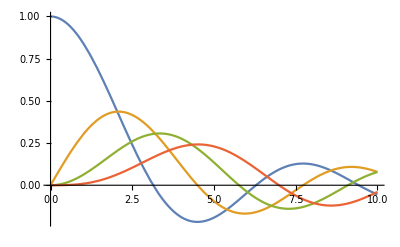

```mathematica
Plot[Evaluate[Table[sbessj[n,x],{n,0,3}]],{x,0,10}]
```

```mathematica
D[sbessj[2,z],z]
```

sbessj^(0,1)[2,z]

```mathematica
?*Q
```

```mathematica
Positive[-2]
```

False

```mathematica
Clear[f];
f[x_?EvenQ]:=x^2;
f[x_?OddQ]:=-x^3
```

```mathematica
f[2]
```

4

```mathematica
f[3]
```

-27

```mathematica
Table[f[n],{n,-5,5}]
```

{125,16,27,4,1,0,-1,4,-27,16,-125}

```mathematica
f[1.5]
```

f[1.5]

```mathematica
Clear[f];
f[x_Integer?Positive]:="I am a positive integer"
f[x_Integer?Negative]:="I am a negative integer"
f[x_Real?Positive]:="I am a positive real number"
f[x_Real?Negative]:="I am a negative real number"
f[x_Symbol]:="I don't know what I am!"
```

```mathematica
f/@{q,14,-27,π,N[π]}
```

{I don't know what I am!,I am a positive integer,I am a negative integer,I don't know what I am!,I am a positive real number}

```mathematica
Clear[f,x];
f[x_?(PrimeQ[#]&&Positive[#]&)]:=1/x
```

```mathematica
f/@{-4,-3,x,16,17,"stuff"}
```

{f[-4],f[-3],f[x],f[16],1/17,f[stuff]}

```mathematica
Clear[h,x,y];
h[x_]:=Integrate[Sin[x+y],{y,0,π}]
```

```mathematica
h[x]
```

2 Cos[x]

```mathematica
h[2]
```

2 Cos[2]

```mathematica
h[y]
```

0

```mathematica
Trace[h[y]]
```

{h[y],∫_0^π Sin[y+y]ⅆy,{{y+y,2 y},Sin[2 y]},∫_0^π Sin[2 y]ⅆy,{{FreeQ[Sin[2 y],HoldPattern[Root[Integrate`ImproperDump`aa$__/;Internal`DependsOnQ[{Integrate`ImproperDump`aa$},y]]]],True},!True,False},∫_0^π Sin[2 y]ⅆy,0}

```mathematica
Clear[h,x,y];
h[x_]:=Module[{y},Integrate[Sin[x+y],{y,0,π}]]
```

```mathematica
h[y]
```

2 Cos[y]

```mathematica
Trace[h[y]]
```

{h[y],Module[{y$},∫_0^π Sin[y+y$]ⅆy$],{∫_0^π Sin[y+y$43655]ⅆy$43655,{{FreeQ[Sin[y+y$43655],HoldPattern[Root[Integrate`ImproperDump`aa$__/;Internal`DependsOnQ[{Integrate`ImproperDump`aa$},y$43655]]]],True},!True,False},∫_0^π Sin[y+y$43655]ⅆy$43655,2 Cos[y]},2 Cos[y]}

```mathematica
Trace[ Module[{seconds},seconds=Round[ AbsoluteTime[] ];SeedRandom[seconds];Random[]] ]
```

{Module[{seconds},seconds=Round[AbsoluteTime[]];SeedRandom[seconds];Random[]],{seconds$43701=Round[AbsoluteTime[]];SeedRandom[seconds$43701];Random[],{{{AbsoluteTime[],3.944296600709941×10^9},Round[3.944296600709941×10^9],3944296601},seconds$43701=3944296601,3944296601},{{seconds$43701,3944296601},SeedRandom[3944296601],$RandomGeneratorState,RandomGeneratorState[…]},{Random[],0.0144397},0.0144397},0.0144397}

```mathematica
Needs["Graphics`PlotField`"];
```

Get::noopen: Cannot open Graphics`PlotField`.

Needs::nocont: Context Graphics`PlotField` was not created when Needs was evaluated.

```mathematica
a = "stuff"; b="more stuff"; c="yet more stuff";
```

```mathematica
ff[x_] := With[{a=2,b=3,c=4}, a x^2+b x + c]
```

```mathematica
ff[x]
```

4+3 x+2 x^2

```mathematica
gg[x_] := With[{a=2,b=3,c=4}, a=12;b=-12;c="junk";a x^2+b x + c]
```

```mathematica
gg[y]
```

Set::setraw: Cannot assign to raw object 2.

Set::setraw: Cannot assign to raw object 3.

Set::setraw: Cannot assign to raw object 4.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

4+3 y+2 y^2

```mathematica
Trace[ff[x]]
```

{ff[x],With[{a$=2,b$=3,c$=4},a$ x^2+b$ x+c$],2 x^2+3 x+4,4+3 x+2 x^2}

```mathematica
Clear[f,x]
```

```mathematica
f[x_]:=Block[{a=2,b=3,c=4}, a x^2+b x + c]
```

```mathematica
{a,b,c}
```

{stuff,more stuff,yet more stuff}

```mathematica
f[x]
```

4+3 x+2 x^2

```mathematica
{a,b,c}
```

{stuff,more stuff,yet more stuff}

```mathematica
Table[a^2,{a,0,4}]
```

{0,1,4,9,16}

```mathematica
a
```

stuff

```mathematica
f[x_]:=Module[{i},Sum[1/x^i,{i,0,5}]]
```

```mathematica
g[x_]:=Block[{i},Sum[1/x^i,{i,0,5}]]
```

```mathematica
{f[2],f[x],f[i]}
```

{63/32,1+1/x^5+1/x^4+1/x^3+1/x^2+1/x,1+1/i^5+1/i^4+1/i^3+1/i^2+1/i}

```mathematica
{g[2],g[x],g[i]}
```

Power::indet: Indeterminate expression 0^0 encountered.

{2,1+1/x^5+1/x^4+1/x^3+1/x^2+1/x,Indeterminate}

```mathematica
Clear[step];
step[x_]:=If[x>0,1,0]
```

```mathematica
{step[-1],step[0],step[2],step[x], step[x-1]/.x->2}
```

{0,0,1,If[x>0,1,0],1}

```mathematica
Clear[f];
f[x_] := If[x>0,1,0,0]
```

```mathematica
{f[-1],f[0],f[2],f[x], f[x-1]/.x->2}
```

{0,0,1,0,0}

```mathematica
Clear[step];
step[x_] := Which[x>0,1,x==0, 1/2, x<0, 0]
```

```mathematica
{step[-1],step[0],step[2],step[x], step[x-1]/.x->2}
```

{0,1/2,1,Which[x>0,1,x==0,1/2,x<0,0],1}

```mathematica
switchfunction[x_]:=Switch[x,
_Integer,FactorInteger[x],
_Rational,N[x],
_Real,Rationalize[x],
_Complex,Im[x],
_Symbol,1+x^2,
_,"The Head is "<>ToString[Head[x]]<>"."]
```

```mathematica
switchfunction/@{12,1/3,9.1,2+7 I,π,"xxx yyy"}
```

{{{2,2},{3,1}},0.333333,91/10,7,1+π^2,The Head is String.}